-Graphics3D-

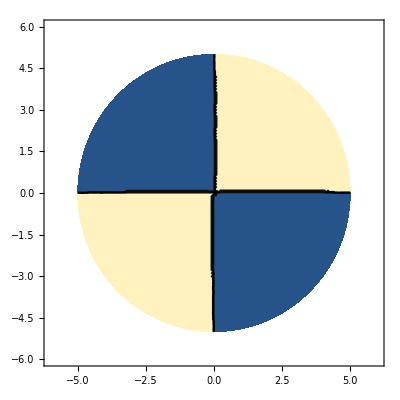

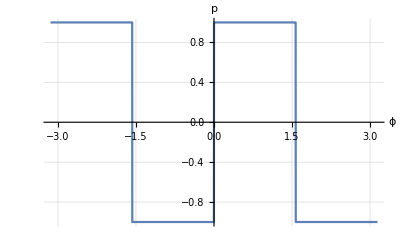

```mathematica
(*R1=1/2*R2;*)
h=1/50*R1;
μ=0.3;
PlotData={p0->1,R->5,Dпл->1};
(*Функция давления*)
p[ρ_,θ_]:=p0*Piecewise[{
{1,-Pi<=θ<-Pi/2},
{-1,-Pi/2<=θ<0},
{1,0<=θ<Pi/2 },
{-1,Pi/2<=θ<Pi},
{1,Pi<=θ<3*Pi/2},
{-1,-Pi<=θ<2*Pi}
}];
(*Штука, превращающая x y в ρ θ*)
ToPolar={ρ->Sqrt[x^2+y^2],θ->ArcTan[y/x]};
(*Нарисуем*)
Plot3D[p[ρ,θ]/.ToPolar/.{p0->1,R1->5},{x,-6,6},{y,-6,6},RegionFunction->Function[{x,y,z},x^2+y^2<=R^2/.PlotData]]
ContourPlot[p[ρ,θ]/.ToPolar/.{p0->1,R1->5},{x,-6,6},{y,-6,6},RegionFunction->Function[{x,y,z},x^2+y^2<=R^2/.PlotData]]
Plot[{p[ρ,θ]/.p0->1},{θ,-Pi,Pi},GridLines->Automatic,AxesLabel->{"ϕ","p"}]
```

-(8 p0 Cos[(k π)/2] Sin[(k π)/4]^2)/(k π)

{(4 p0)/π,(4 p0)/(3 π),(4 p0)/(5 π),(4 p0)/(7 π),(4 p0)/(9 π)}

(4 p0 Sin[2 θ])/π+(4 p0 Sin[6 θ])/(3 π)+(4 p0 Sin[10 θ])/(5 π)+(4 p0 Sin[14 θ])/(7 π)+(4 p0 Sin[18 θ])/(9 π)

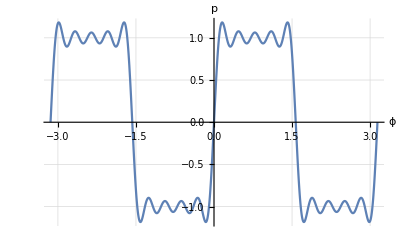

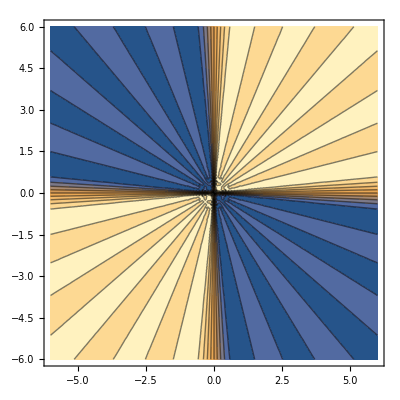

```mathematica
(*Разложим в ряд, но ручками*)
NElements=4;                   (*Количество значащих членов*)
Step=4;                              (*Шаг. Это чтобы пропускать нулевые решения. При такой нагрузке не трогай*)
Coeff2[i_]=1/Pi*Integrate[p[ρ,θ]*Sin[k*θ],{θ,-Pi,Pi}]/.k->i//Simplify;
Coeff2[k]
Coeffs2=Map[Coeff2,Range[2,2+NElements*Step,Step]]

Mno2[i_]=Sin[i*θ]//Simplify;
Mnos2=Map[Mno2,Range[2,2+NElements*Step,Step]];
pSeries=Coeffs2.Mnos2
Plot[{pSeries/.p0->1},{θ,-Pi,Pi},GridLines->Automatic,AxesLabel->{"ϕ","p"}]
ContourPlot[pSeries/.ToPolar/.{p0->1,R1->5},{x,-6,6},{y,-6,6}]
```

```mathematica
(*Возьмем решение в виде суммы*)
(*Это единичное слагаемое*)
Wkk[ρ,θ]=Wk[ρ]*Sin[k*θ];
(*Подставим в исходное уравнение и разделим на синус*)
expr[i_]=Laplacian[Laplacian[Wkk[ρ,θ],{ρ,θ},"Polar"],{ρ,θ},"Polar"]/Sin[θ*k]/.k->i//Expand;
expr[k]
```

-(4 k^2 Wk[ρ])/ρ^4+(k^4 Wk[ρ])/ρ^4+Wk'[ρ]/ρ^3+(2 k^2 Wk'[ρ])/ρ^3-Wk''[ρ]/ρ^2-(2 k^2 Wk''[ρ])/ρ^2+(2 Wk^(3)[ρ])/ρ+Wk^(4)[ρ]

```mathematica
(*Получаем ДУ для коэффициентов*)
eq[i_]=expr[i]==Coeff2[i]/Dпл;
equations=Map[eq,Range[2,2+NElements*Step,Step]]
```

{(9 Wk'[ρ])/ρ^3-(9 Wk''[ρ])/ρ^2+(2 Wk^(3)[ρ])/ρ+Wk^(4)[ρ]==(4 p0)/(Dпл π),(1152 Wk[ρ])/ρ^4+(73 Wk'[ρ])/ρ^3-(73 Wk''[ρ])/ρ^2+(2 Wk^(3)[ρ])/ρ+Wk^(4)[ρ]==(4 p0)/(3 Dпл π),(9600 Wk[ρ])/ρ^4+(201 Wk'[ρ])/ρ^3-(201 Wk''[ρ])/ρ^2+(2 Wk^(3)[ρ])/ρ+Wk^(4)[ρ]==(4 p0)/(5 Dпл π),(37632 Wk[ρ])/ρ^4+(393 Wk'[ρ])/ρ^3-(393 Wk''[ρ])/ρ^2+(2 Wk^(3)[ρ])/ρ+Wk^(4)[ρ]==(4 p0)/(7 Dпл π),(103680 Wk[ρ])/ρ^4+(649 Wk'[ρ])/ρ^3-(649 Wk''[ρ])/ρ^2+(2 Wk^(3)[ρ])/ρ+Wk^(4)[ρ]==(4 p0)/(9 Dпл π)}

```mathematica
(*Решения этих ДУ с неизвестными константами*)
sol[i_]=DSolve[eq[i],Wk[ρ],ρ]/.{C[1]->0,C[2]->0}//First
DSolve[eq[k],Wk[ρ],ρ]//First
sol2=DSolve[eq[2],Wk[ρ],ρ]/.{C[1]->0,C[4]->0}/.{C[2]->C[4]};
solutions=Join[sol2,Map[sol,Range[6,2+NElements*Step,Step]]]
(*sol2=DSolve[{eq[2],Wk[R]==0,Wk'[R]==0,Wk[0]==0},Wk[ρ],ρ]*)
(*solutions/.{C[2]->0,C[4]->0}*)
DSolve[eq[i],Wk[ρ],ρ]
```

{Wk[ρ]→ρ^(2+i) C[3]+ρ^i C[4]-(8 p0 ρ^4 Cos[(i π)/2] Sin[(i π)/4]^2)/(Dпл (-4+i) (-2+i) i (2+i) (4+i) π)}

{Wk[ρ]→ρ^-k C[1]+ρ^(2-k) C[2]+ρ^(2+k) C[3]+ρ^k C[4]-(8 p0 ρ^4 Cos[(k π)/2] Sin[(k π)/4]^2)/(Dпл (-4+k) (-2+k) k (2+k) (4+k) π)}

{{Wk[ρ]→-(11 p0 ρ^4)/(144 Dпл π)+1/4 ρ^4 C[3]+1/2 ρ^2 C[4]+(p0 ρ^4 Log[ρ])/(12 Dпл π)},{Wk[ρ]→(p0 ρ^4)/(480 Dпл π)+ρ^8 C[3]+ρ^6 C[4]},{Wk[ρ]→(p0 ρ^4)/(10080 Dпл π)+ρ^12 C[3]+ρ^10 C[4]},{Wk[ρ]→(p0 ρ^4)/(60480 Dпл π)+ρ^16 C[3]+ρ^14 C[4]},{Wk[ρ]→(p0 ρ^4)/(221760 Dпл π)+ρ^20 C[3]+ρ^18 C[4]}}

{{Wk[ρ]→ρ^-i C[1]+ρ^(2-i) C[2]+ρ^(2+i) C[3]+ρ^i C[4]-(8 p0 ρ^4 Cos[(i π)/2] Sin[(i π)/4]^2)/(Dпл (-4+i) (-2+i) i (2+i) (4+i) π)}}

```mathematica
(*Зададим граничные условия*)

beq1[k_]:=((Wk[ρ]/.solutions)[[k]]/.{ρ->R})==0/.{ρ->R};
beq2[k_]:=D[((Wk[ρ]/.solutions)[[k]]),ρ]==0/.{ρ->R};
(*Найдем константы*)
const[k_]:=Solve[{beq1[k],beq2[k]},{C[3],C[4]}]//First
constants=Map[const,Range[1,NElements+1,1]]
```

{{C[3]→-(p0 (-5+12 Log[R]))/(36 Dпл π),C[4]→(p0 R^2)/(12 Dпл π)},{C[3]→p0/(480 Dпл π R^4),C[4]→-p0/(240 Dпл π R^2)},{C[3]→p0/(3360 Dпл π R^8),C[4]→-p0/(2520 Dпл π R^6)},{C[3]→p0/(12096 Dпл π R^12),C[4]→-p0/(10080 Dпл π R^10)},{C[3]→p0/(31680 Dпл π R^16),C[4]→-p0/(27720 Dпл π R^14)}}

```mathematica
(*Теперь подставим константы в полученные решения*)
```

```mathematica
solres[k_]:=solutions[[k]]/.constants[[k]];
solutionsres=Map[solres,Range[1,NElements+1,1]]
```

{{Wk[ρ]→(p0 R^2 ρ^2)/(24 Dпл π)-(11 p0 ρ^4)/(144 Dпл π)-(p0 ρ^4 (-5+12 Log[R]))/(144 Dпл π)+(p0 ρ^4 Log[ρ])/(12 Dпл π)},{Wk[ρ]→(p0 ρ^4)/(480 Dпл π)-(p0 ρ^6)/(240 Dпл π R^2)+(p0 ρ^8)/(480 Dпл π R^4)},{Wk[ρ]→(p0 ρ^4)/(10080 Dпл π)-(p0 ρ^10)/(2520 Dпл π R^6)+(p0 ρ^12)/(3360 Dпл π R^8)},{Wk[ρ]→(p0 ρ^4)/(60480 Dпл π)-(p0 ρ^14)/(10080 Dпл π R^10)+(p0 ρ^16)/(12096 Dпл π R^12)},{Wk[ρ]→(p0 ρ^4)/(221760 Dпл π)-(p0 ρ^18)/(27720 Dпл π R^14)+(p0 ρ^20)/(31680 Dпл π R^16)}}

```mathematica
(*А теперь не подстановками, а прям функции и прямо суммами и прям ваще*)
Wk[ρ]/.solutionsres;
sinuses=Sin[#*θ]&/@(Range[2,2+NElements*Step,Step]); (*Какая-то магическая конструкция, украденная из хелпа. Но работает!*)
W[ρv_,θv_]=((Wk[ρ]/.solutionsres).sinuses)/.{ρ->ρv,θ->θv};
W[ρ,θ] (*А вот и результат!*)
```

((p0 R^2 ρ^2)/(24 Dпл π)-(11 p0 ρ^4)/(144 Dпл π)-(p0 ρ^4 (-5+12 Log[R]))/(144 Dпл π)+(p0 ρ^4 Log[ρ])/(12 Dпл π)) Sin[2 θ]+((p0 ρ^4)/(480 Dпл π)-(p0 ρ^6)/(240 Dпл π R^2)+(p0 ρ^8)/(480 Dпл π R^4)) Sin[6 θ]+((p0 ρ^4)/(10080 Dпл π)-(p0 ρ^10)/(2520 Dпл π R^6)+(p0 ρ^12)/(3360 Dпл π R^8)) Sin[10 θ]+((p0 ρ^4)/(60480 Dпл π)-(p0 ρ^14)/(10080 Dпл π R^10)+(p0 ρ^16)/(12096 Dпл π R^12)) Sin[14 θ]+((p0 ρ^4)/(221760 Dпл π)-(p0 ρ^18)/(27720 Dпл π R^14)+(p0 ρ^20)/(31680 Dпл π R^16)) Sin[18 θ]

-Graphics3D-

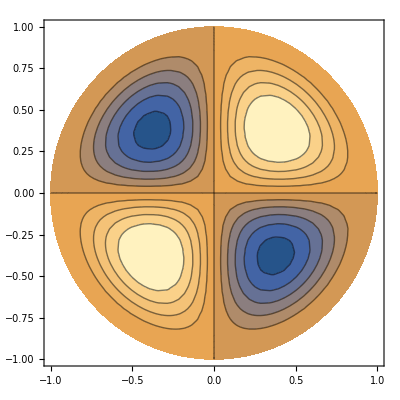

-(0.0630303 p0)/Dпл+(0.0102888 p0)/(Dпл R^16)-(0.00587932 p0)/(Dпл R^14)-(0.00673672 p0)/(Dпл R^12)+(0.00404203 p0)/(Dпл R^10)+(0.00606305 p0)/(Dпл R^8)-(0.00404203 p0)/(Dпл R^6)-(0.0106103 p0)/(Dпл R^4)+(0.0106103 p0)/(Dпл R^2)+(0.0265258 p0 R^2)/Dпл-(0.00884194 p0 (-5.+12. Log[R]))/Dпл

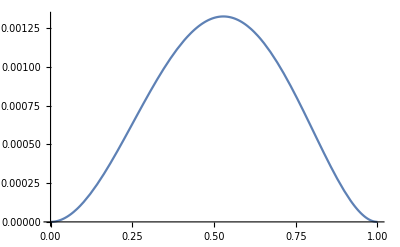

```mathematica
(*Нарисуем!*)
PlotData={p0->1,R->1,Dпл->1};
Plot3D[W[ρ,θ]/.ToPolar/.PlotData,{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,z},x^2+y^2<=R^2/.PlotData],AxesLabel->{"X","Y","W"}]
ContourPlot[W[ρ,θ]/.ToPolar/.PlotData,{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,z},x^2+y^2<=R^2/.PlotData],PlotRange->{-0.00135,0.00135},Contours->10]
W[ρ,θ]/.ToPolar/.{x->1,y->1}//N
Plot[W[ρ,Pi/4]/.PlotData,{ρ,0,R/.PlotData}]
```

(p0 ρ^4 (-1+R^2/ρ^2+2 Log[ρ/R]) Sin[2 θ])/(24 Dпл π)+((p0 ρ^4)/(480 Dпл π)-(p0 ρ^6)/(240 Dпл π R^2)+(p0 ρ^8)/(480 Dпл π R^4)) Sin[6 θ]+((p0 ρ^4)/(26880 Dпл π)-(p0 ρ^12)/(5376 Dпл π R^8)+(p0 ρ^14)/(6720 Dпл π R^10)) Sin[12 θ]+((p0 ρ^4)/(221760 Dпл π)-(p0 ρ^18)/(27720 Dпл π R^14)+(p0 ρ^20)/(31680 Dпл π R^16)) Sin[18 θ]+((p0 ρ^4)/(960960 Dпл π)-(p0 ρ^24)/(87360 Dпл π R^20)+(p0 ρ^26)/(96096 Dпл π R^22)) Sin[24 θ]

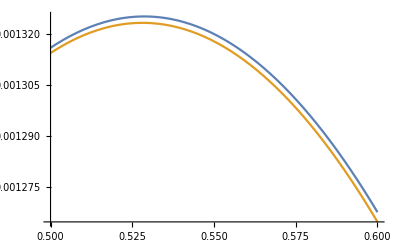

```mathematica
(*То, что написано в отчете*)
Wot[ρ_,θ_]=Sin [2*θ]*p0*ρ^4/(24*Dпл*Pi)*(R^2/ρ^2-1+2*Log[ρ/R])+Sum[Sin [k*θ]*(4*p0*R^(2-k)*ρ^(2+k)/(Pi*Dпл*(k^4+4*k^3-4*k^2-16*k))-4*p0*R^(4-k)*ρ^k/(Pi*Dпл*(k^4+2*k^3-16*k^2-32*k))+8*p0*ρ^4/(Pi*Dпл*(k^5-20*k^3+64*k)))/.k->6*i
,{i,4}]
Plot[{W[ρ,Pi/4]/.PlotData,Wot[ρ,Pi/4]/.PlotData},{ρ,0.5,0.6}]
```

```mathematica
Mρ[ρ_,θ_]=-Dпл*(D[W[ρ,θ],{ρ,2}]+μ*(1/ρ*D[W[ρ,θ],{ρ,1}]+1/ρ^2*D[W[ρ,θ],{θ,2}]))//Simplify
Mθ[ρ_,θ_]=-Dпл*(1/ρ*D[W[ρ,θ],{ρ,1}]+1/ρ^2*D[W[ρ,θ],{θ,2}]+μ*D[W[ρ,θ],{ρ,2}])//Simplify;
Mρθ[ρ_,θ_]=(1-μ)*Dпл*(1/ρ*D[D[W[ρ,θ],{θ,1}],{ρ,1}]-1/ρ^2*D[W[ρ,θ],{θ,1}])//Simplify;
Mρθ[ρ_,θ_]=(1-μ)*Dпл*D[(1/ρ*D[W[ρ,θ],θ]),ρ]//Simplify; (*То же самое, что и выше*)
Plot3D[Mρ[ρ,θ]/.ToPolar/.PlotData,{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,z},x^2+y^2<=R^2/.PlotData],AxesLabel->{"X","Y","Mρ"}]
Plot3D[Mθ[ρ,θ]/.ToPolar/.PlotData,{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,z},x^2+y^2<=R^2/.PlotData],AxesLabel->{"X","Y","Mθ"}]
Plot3D[Mρθ[ρ,θ]/.ToPolar/.PlotData,{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,z},x^2+y^2<=R^2/.PlotData],AxesLabel->{"X","Y","Mρθ"}]

(*ContourPlot[W[ρ,θ]/.ToPolar/.PlotData,{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,z},x^2+y^2<=R^2/.PlotData],PlotRange->{-0.00135,0.00135},Contours->10]*)
```

p0 (-0.0185681 R^2-0.0344836 ρ^2+0.31831 ρ^2 Log[R]-0.31831 ρ^2 Log[ρ]) Sin[2 θ]+1/R^16 p0 ρ^2 (R^12 (-0.00159155 R^4+0.0278521 R^2 ρ^2-0.0315657 ρ^4) Sin[6 θ]+R^8 (0.000530516 R^8+0.00795775 R^2 ρ^6-0.010004 ρ^8) Sin[10 θ]+0.000239996 R^16 Sin[14 θ]+0.00402308 R^6 ρ^10 Sin[14 θ]-0.00489465 R^4 ρ^12 Sin[14 θ]+0.000120572 R^16 Sin[18 θ]+0.00245967 R^2 ρ^14 Sin[18 θ]-0.00290176 ρ^16 Sin[18 θ])

-Graphics3D-

-Graphics3D-

-Graphics3D-

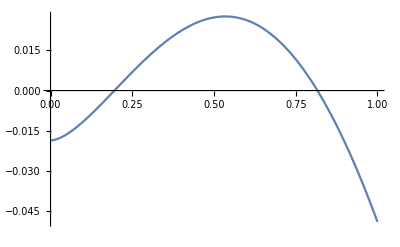

0.-0.0489522 p0 R^2

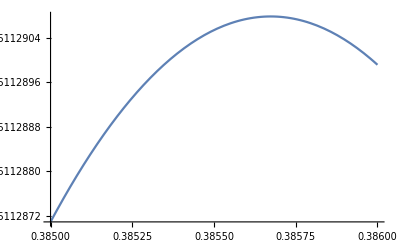

0.0251129 p0 R^2

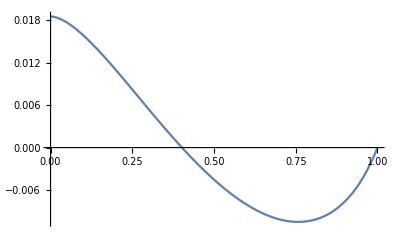

0.0185681 p0 R^2

```mathematica
Plot[{Mρ[ρ,Pi/4]/.ToPolar/.PlotData},{ρ,0,1}]
Limit[Mρ[ρ,Pi/4],ρ->R]
Plot[{Mθ[ρ,Pi/4]/.ToPolar/.PlotData},{ρ,0.385,0.386}]
Limit[Mθ[ρ,Pi/4],ρ->0.385*R]
Plot[{Mρθ[ρ,0]/.ToPolar/.PlotData},{ρ,0,1}]
Limit[Mρθ[ρ,0],ρ->0]
```

(p0 R^2 ρ^2 Sin[2 θ])/(24 Dпл π)

(p0 R^2 ρ^2)/(24 Dпл π)

-0.0371362 p0 R^2 Cos[θ] Sin[θ]

(p0 ρ^2 Cos[θ] Sin[θ])/π

-0.31831 p0 ρ^2 (0.608333+Log[ρ/R]) Sin[2 θ]

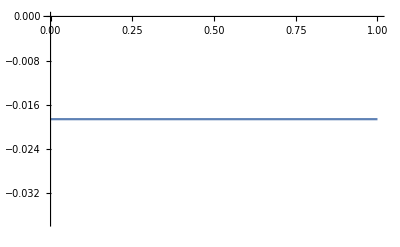

-0.0185681

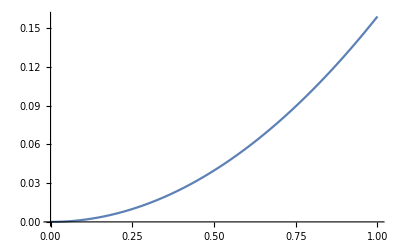

0

-Graphics-

0.

```mathematica
Wot1[ρ_,θ_]=Sin [2*θ]*p0*ρ^4/(24*Dпл*Pi)*(R^2/ρ^2)
Wot1[ρ,Pi/4]
Wot2[ρ_,θ_]=Sin [2*θ]*p0*ρ^4/(24*Dпл*Pi)*(-1);
Wot3[ρ_,θ_]=Sin [2*θ]*p0*ρ^4/(24*Dпл*Pi)*(2*Log[ρ/R]);
(*+Sum[Sin [k*θ]*(4*p0*R^(2-k)*ρ^(2+k)/(Pi*Dпл*(k^4+4*k^3-4*k^2-16*k))-4*p0*R^(4-k)*ρ^k/(Pi*Dпл*(k^4+2*k^3-16*k^2-32*k))+8*p0*ρ^4/(Pi*Dпл*(k^5-20*k^3+64*k)))/.k->6*i
,{i,4}]*)
Motρ1[ρ_,θ_]=-Dпл*(D[Wot1[ρ,θ],{ρ,2}]+μ*(1/ρ*D[Wot1[ρ,θ],{ρ,1}]+1/ρ^2*D[Wot1[ρ,θ],{θ,2}]))//Simplify
Motρ2[ρ_,θ_]=-Dпл*(D[Wot2[ρ,θ],{ρ,2}]+μ*(1/ρ*D[Wot2[ρ,θ],{ρ,1}]+1/ρ^2*D[Wot2[ρ,θ],{θ,2}]))//Simplify
Motρ3[ρ_,θ_]=-Dпл*(D[Wot3[ρ,θ],{ρ,2}]+μ*(1/ρ*D[Wot3[ρ,θ],{ρ,1}]+1/ρ^2*D[Wot3[ρ,θ],{θ,2}]))//Simplify
Motθ1[ρ_,θ_]=-Dпл*(1/ρ*D[Wot[ρ,θ],{ρ,1}]+1/ρ^2*D[Wot[ρ,θ],{θ,2}]+μ*D[Wot[ρ,θ],{ρ,2}])//Simplify;
Motρθ1[ρ_,θ_]=(1-μ)*Dпл*(1/ρ*D[D[Wot[ρ,θ],{θ,1}],{ρ,1}]-1/ρ^2*D[Wot[ρ,θ],{θ,1}])//Simplify;
Plot[{Motρ1[ρ,Pi/4]/.ToPolar/.PlotData},{ρ,0,1}]
Limit[Motρ1[ρ,Pi/4]/.PlotData,ρ->0]
Plot[{Motρ2[ρ,Pi/4]/.ToPolar/.PlotData},{ρ,0,1}]
Limit[Motρ2[ρ,Pi/4]/.PlotData,ρ->0]
Plot[{Motρ3[ρ,Pi/4]/.ToPolar/.PlotData},{ρ,0,1}]
Limit[Motρ3[ρ,Pi/4]/.PlotData,ρ->0]
(*Plot3D[Motρ[ρ,θ]/.ToPolar/.PlotData,{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,z},x^2+y^2<=R^2/.PlotData],AxesLabel->{"X","Y","Mρ"}]
Plot3D[Motθ[ρ,θ]/.ToPolar/.PlotData,{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,z},x^2+y^2<=R^2/.PlotData],AxesLabel->{"X","Y","Mθ"}]
Plot3D[Motρθ[ρ,θ]/.ToPolar/.PlotData,{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,z},x^2+y^2<=R^2/.PlotData],AxesLabel->{"X","Y","Mρθ"}]*)
```

```mathematica
(9 Wk'[ρ])/ρ^3-(9 Wk''[ρ])/ρ^2+(2 Derivative[3][Wk][ρ])/ρ+Derivative[4][Wk][ρ]==(-4 p0)/(Dпл π)
DSolve[(9 Wk'[ρ])/ρ^3-(9 Wk''[ρ])/ρ^2+(2 Derivative[3][Wk][ρ])/ρ+Derivative[4][Wk][ρ]==(-4 p0)/(Dпл π),Wk[ρ],ρ]
```

(9 Wk'[ρ])/ρ^3-(9 Wk''[ρ])/ρ^2+(2 Wk^(3)[ρ])/ρ+Wk^(4)[ρ]==-(4 p0)/(Dпл π)

{{Wk[ρ]→(11 p0 ρ^4)/(144 Dпл π)-C[1]/(2 ρ^2)+1/2 ρ^2 C[2]+1/4 ρ^4 C[3]+C[4]-(p0 ρ^4 Log[ρ])/(12 Dпл π)}}

```mathematica
(9 Wk'[ρ])/ρ^3-(9 Wk''[ρ])/ρ^2+(2 Derivative[3][Wk][ρ])/ρ+Derivative[4][Wk][ρ]==0/.{Wk[ρ]->ρ^m,Wk'[ρ]->m*ρ^(m-1),Wk''[ρ]->m*(m-1)*ρ^(m-2),Wk'''[ρ]->m*(m-1)*(m-2)*ρ^(m-3),Wk''''[ρ]->m*(m-1)*(m-2)*(m-3)*ρ^(m-4)}//Expand
```

16 m ρ^(-4+m)-4 m^2 ρ^(-4+m)-4 m^3 ρ^(-4+m)+m^4 ρ^(-4+m)==0

```mathematica
Solve[m^4-4*m^3-4*m^2+16*m==0]
```

{{m→-2},{m→0},{m→2},{m→4}}

```mathematica
m^4+2*m^3-9*m^2+9*m/.m->2
```

14

```mathematica
Wч[ρ_]=A*ρ^4*Log[ρ/R]
Wч''''[ρ]+2/ρ*Wч'''[ρ]-9/ρ^2*Wч''[ρ]+9/ρ^3*Wч'[ρ]//Expand
Solve[Wч''''[ρ]+2/ρ*Wч'''[ρ]-9/ρ^2*Wч''[ρ]+9/ρ^3*Wч'[ρ]==-4*p0/(Pimod*Dmod),A]
```

A ρ^4 Log[ρ/R]

48 A

{{A→-p0/(12 Dmod Pimod)}}